```mathematica
f=(1/Sqrt[Pi])*(2/a0)^(3/2)*Exp[-2r1/a0]*(1/Sqrt[Pi])*(2/a0)^(3/2)*Exp[-2r2/a0]
```

(8 ⅇ^(-(2 r1)/a0-(2 r2)/a0))/(a0^3 π)

```mathematica
e^2*Integrate[f^2*1/Sqrt[r1^2+r2^2-2r1*r2*Cos[t2]]*r2^2*Sin[t2]*r1^2*Sin[t1],{r1,0,Infinity},{r2,0,Infinity},{t1,0,Pi},{t2,0,Pi},{p1,0,2*Pi},{p2,0,2*Pi}]
```

ConditionalExpression[(5 e^2)/(4 a0), Re[a0]>0]

```mathematica
g=(1/Sqrt[Pi])*(Z/a0)^(3/2)*Exp[-Z*r1/a0]*(1/Sqrt[Pi])*(Z/a0)^(3/2)*Exp[-Z*r2/a0]
```

(ⅇ^(-(r1 Z)/a0-(r2 Z)/a0) Z^3)/(a0^3 π)

```mathematica
first=
```

```mathematica
e^2*Integrate[g^2*(Z-2)/r1*r2^2*Sin[t2]*r1^2*Sin[t1],{r1,0,Infinity},{r2,0,Infinity},{t1,0,Pi},{t2,0,Pi},{p1,0,2*Pi},{p2,0,2*Pi},Assumptions->{Z/a0>0}]
```

(e^2 (-2+Z) Z)/a0

```mathematica
third=e^2*Integrate[g^2*1/Sqrt[r1^2+r2^2-2r1*r2*Cos[t2]]*r2^2*Sin[t2]*r1^2*Sin[t1],{r1,0,Infinity},{r2,0,Infinity},{t1,0,Pi},{t2,0,Pi},{p1,0,2*Pi},{p2,0,2*Pi},Assumptions->{Z/a0>0}]
```

(5 e^2 Z)/(8 a0)

```mathematica
h[Z_]:=-Z^2+(5 Z)/8+2Z(Z-2);
```

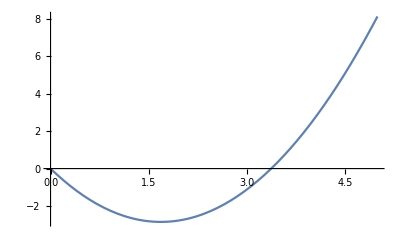

```mathematica
Plot[h[z],{z,0,5}]
```

```mathematica
Solve[D[h[z],z]==0,z]
```

{{z→27/16}}

```mathematica
h[27/16]
```

-729/256

```mathematica
N[27/16]
```

1.6875